```mathematica
Limit[Sin[x]/x,x->0]
```

1

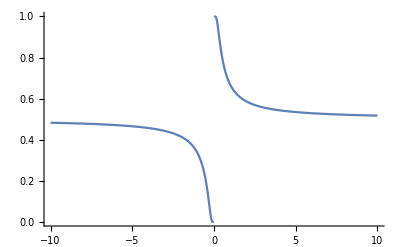

```mathematica
Plot[1/(1+2^(-1/x)),{x,-10,10},PlotRange->All]
```

```mathematica
Limit[1/(1+2^(-1/x)),x->0]
```

Indeterminate

```mathematica
Limit[1/(1+2^(-1/x)),x->0,Direction->"FromAbove"]
```

1

```mathematica
Limit[1/(1+2^(-1/x)),x->0,Direction->"FromBelow"]
```

0

```mathematica
Limit[n-√(n+1) √(n+3),n->Infinity]
```

-2

```mathematica
Limit[n-√(n+1) √(n+3),n->∞]
```

-2

```mathematica
Sum[i^2,{i,1,10}]
```

385

```mathematica
Sum[n/(n^4+n^2+1),{n,1,∞}]
```

1/2

```mathematica
Product[i^2,{i,1,10}]
```

13168189440000

```mathematica
f[x_]:=Cos[x] x^6
```

```mathematica
f'[x]
```

6 x^5 Cos[x]-x^6 Sin[x]

```mathematica
(f^(5))[x]
```

f^5[x]

```mathematica
D[f[x],x]
```

6 x^5 Cos[x]-x^6 Sin[x]

```mathematica
D[f[x],{x,5}]
```

720 x Cos[x]-1200 x^3 Cos[x]+30 x^5 Cos[x]-1800 x^2 Sin[x]+300 x^4 Sin[x]-x^6 Sin[x]

```mathematica
fDerivative5[x_]:=D[f[x],{x,5}]
```

```mathematica
fDerivative5[5]
```

General::ivar: 5 is not a valid variable.

```mathematica
D[(15625 Cos[5]), {5,5}]
```

```mathematica
ff[x_,y_]:=x^2+y^2
```

```mathematica
D[ff[x,y],{x,1}]
```

2 x

```mathematica
Clear[fDerivative5]
```

```mathematica
fDerivative5[x_]=D[f[x],{x,5}]
```

720 x Cos[x]-1200 x^3 Cos[x]+30 x^5 Cos[x]-1800 x^2 Sin[x]+300 x^4 Sin[x]-x^6 Sin[x]

```mathematica
fDerivative5[5]
```

-52650 Cos[5]+126875 Sin[5]

```mathematica
D[f[x],{x,5}]/.x->5
```

-52650 Cos[5]+126875 Sin[5]

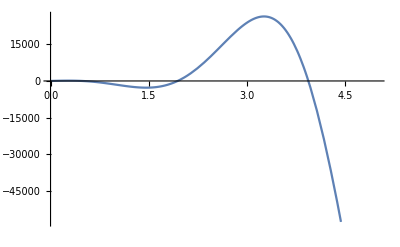

```mathematica
Plot[D[f[x],{x,5}]/.x->xx,{xx,0,5}]
```

```mathematica
Series[E^x Cos[x],{x,0,5}]
```

1+x-x^3/3-x^4/6-x^5/30+O[x]^6

```mathematica
Normal[Series[E^x Cos[x],{x,0,5}]]
```

1+x-x^3/3-x^4/6-x^5/30

```mathematica
Minimize[2 x^2-3 x+5,x]
```

{31/8,{x→3/4}}

```mathematica
g[x_]:=(2 x^2+5 x-1)/(x^2+1)
```

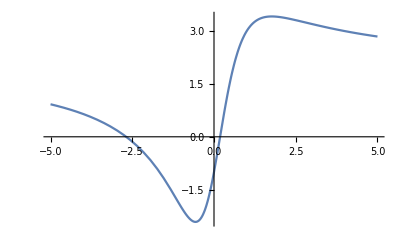

```mathematica
Plot[g[x],{x,-5,5}]
```

```mathematica
Maximize[g[x],x]
```

{(2+√34+2/25 (3+√34)^2)/(1+1/25 (3+√34)^2),{x→1/5 (3+√34)}}

```mathematica
NMaximize[g[x],x]
```

{3.41548,{x→1.76619}}

```mathematica
NMinimize[g[x],x]
```

{-2.41548,{x→-0.56619}}

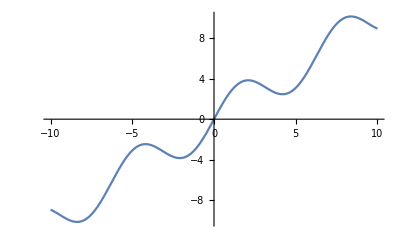

```mathematica
Plot[x+2 Sin[x],{x,-10,10}]
```

```mathematica
Maximize[x+2 Sin[x],x]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{x→∞}}

```mathematica
Maximize[x+2 Sin[x],-10≤x≤10,x]//N
```

{10.1096,{x→8.37758}}

```mathematica
NMaximize[{x+2 Sin[x],-10≤x≤10},x]
```

{10.1096,{x→8.37758}}

```mathematica
FindMaximum[x+2 Sin[x],{x,0,5}]
```

{3.82645,{x→2.0944}}

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Integrate[1/(x^3+1),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

```mathematica
NIntegrate[1/(x^3+1),{x,0,1}]
```

0.835649

```mathematica
Integrate[1/(x^3+1),{x,0,1}]//N
```

0.835649

```mathematica
Integrate[Sin[x]/Log[x],x]
```

∫Sin[x]/Log[x]ⅆx

```mathematica
Integrate[Sin[x]/Log[x],{x,2,5}]
```

∫_2^5 Sin[x]/Log[x]ⅆx

```mathematica
NIntegrate[Sin[x]/Log[x],{x,2,5}]
```

-0.20523

```mathematica
Integrate[Log[y]/(x y),{x,1,5},{y,2,4}]
```

3/2 Log[2]^2 Log[5]

```mathematica
Clear[f]
```

```mathematica
(* Task1 *)
f[x_]:=x^3-Cos[x] √(2 x-8)
```

```mathematica
f'[x]
```

3 x^2-Cos[x]/(√(-8+2 x))+√(-8+2 x) Sin[x]

```mathematica
Limit[(f[x+h]-f[x])/h,h->0]
```

3 x^2+(-Cos[x]+2 (-4+x) Sin[x])/(√2 √(-4+x))

```mathematica
Factor[3 x^2-Cos[x]/(√(-8+2 x))+√(-8+2 x) Sin[x]]
```

(6 √(-4+x) x^2-√2 Cos[x]-8 √2 Sin[x]+2 √2 x Sin[x])/(2 √(-4+x))

```mathematica
Factor[3 x^2+(-Cos[x]+2 (-4+x) Sin[x])/(√2 √(-4+x))]
```

(6 √(-4+x) x^2-√2 Cos[x]-8 √2 Sin[x]+2 √2 x Sin[x])/(2 √(-4+x))

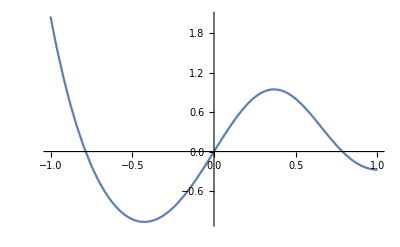

```mathematica
(* Task2 *)
Plot[Sin[4 x]/(E^(x^3)),{x,-1,1}]
```

```mathematica
Minimize[√((x+0.5)^2+(Sin[4 x]/(E^(x^3))+0.5)^2),x]
```

{0.189042,{x→-0.684132}}

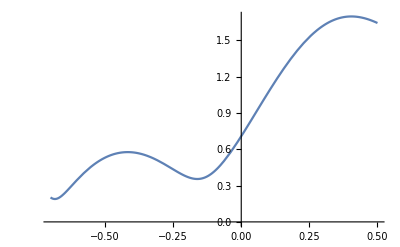

```mathematica
Plot[√((x+0.5)^2+(Sin[4 x]/(E^(x^3))+0.5)^2),{x,-0.7,0.5}]
```

```mathematica
√((x+0.5)^2+(Sin[4 x]/(E^(x^3))+0.5)^2)/.x->-0.6841312
```

0.189042

```mathematica
Manipulate[Show[
Plot[x^k,{x,0,2},PlotRange->{{0,2},{0,2}}],Plot[x,{x,0,2}]],{k,1,10}]
```

```mathematica
Normal[Series[x^5-Cos[x],{x,0,5}]]
```

-1+x^2/2-x^4/24+x^5

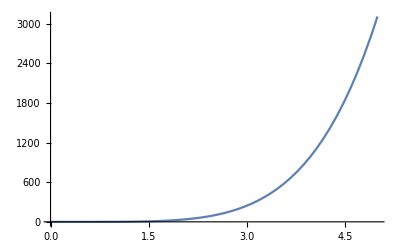

```mathematica
Plot[Normal[Series[x^5-Cos[x],{x,0,5}]]/.x->xx,{xx,0,5}]
```

```mathematica
(* Task3 *)
Manipulate[
Show[
{
Plot[Sin[x]+Cos[x],{x,0,10},PlotStyle->Red],
Plot[Normal[Series[Sin[x]+Cos[x],{x,0,k}]]/.x->xx,
{xx,0,10}]}],
{k,0,30,1}
]
```